## Задание №1-3

```mathematica
Remove /@ Names[$Context <> "*"];
Print["Задание 1"];
P=((R*T)/(V-b))-a/(V+с)^2; 
Print[P, " = P"];
Print["Задание 2"];
f=((R*T)/(V-b))-a/(V+с)^2-p; 
equation=FullSimplify[Solve[f==0,p]];
Print[f," = 0 "];
Print["Задание 3"];
dfdV=D[f,V];
dfdp=D[f,p];
dfdT=D[f,T];
dpdV=FullSimplify[-dfdV/dfdp];
Print["dp/dV = ",dpdV];
dpdT=FullSimplify[-dfdT/dfdp];Print["dp/dT = ",dpdT];
dVdT=FullSimplify[-dfdT/dfdV];Print["dV/dT = ",dVdT];
d2pdV2=FullSimplify[D[dpdV,V]];Print["d2p/dV2 = ",d2pdV2];
```

Задание 1

-a/(с+V)^2+(R T)/(-b+V) = P

Задание 2

-p-a/(с+V)^2+(R T)/(-b+V) = 0

Задание 3

dp/dV = -(R T)/(b-V)^2+(2 a)/(с+V)^3

dp/dT = R/(-b+V)

dV/dT = -(R (b-V) (с+V)^3)/(-2 a (b-V)^2+R T (с+V)^3)

d2p/dV2 = -(6 a)/(с+V)^4+(2 R T)/(-b+V)^3

Null

## Задание №4

```mathematica
Print["Задание 4"];
Cp=0.2*Vc; 
fc=FullSimplify[f/. {V->Vc,p->pc,T->Tc,с->Cp}];
dpdVc=FullSimplify[dpdV/. {V->Vc,p->pc,T->Tc, с->Cp}];
d2pdV2c=FullSimplify[d2pdV2/. {V->Vc,p->pc,T->Tc,с->Cp}];
Function1=FullSimplify[Solve[{dpdVc==0,d2pdV2c==0,fc==0},{a,b,R}]];
a=First[a/. Function1];Print["a = ",a];
b=First[b/. Function1];Print["b = ",b];
R=First[R/. Function1]; Print["R = ",R];
```

Задание 4

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

a = 4.32 pc Vc^2

b = 0.2 Vc

R = (3.2 pc Vc)/Tc

## Задание №5

```mathematica
Print["Задание 5"];
z=R*Tc/(Vc*pc);
Print["z = ",z];
```

Задание 5

z = 3.2

## Задание №6

```mathematica
Print["Задание 6"];
с=Cp;
p=psh*pc;
V=Vsh*Vc;
T=Tsh*Tc;
psh=First[psh/. FullSimplify[Solve[f==0,psh]]];
Print["p' = ",psh];
```

Задание 6

p' = 0.-(3.2 Tsh)/(0.2-1. Vsh)-4.32/(0.2+1. Vsh)^2

## Задание №7

Задание 7

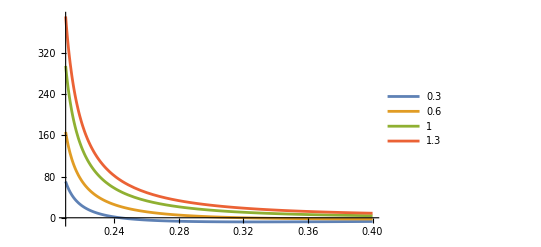

```mathematica
Print["Задание 7"];
Tsh={0.3,0.6,1,1.3};
Plot[psh,{Vsh,0.21,0.4},PlotRange->All, PlotLegends->{0.3, 0.6, 1, 1.3}, PlotStyle->RandomColor,Evaluated->True]
```